# New Channel Transpiration Final Values

```mathematica
ClearAll["Global`*"]
```

## All Velocity Field Terms

```mathematica
v1[y_]:=k ⅇ^(-k y) y 
w1[y_]:=ⅇ^(-k y) (-1+k y)
u1[y_]:=-(ⅇ^(-k y)  y (1+k y))/(4 k)
um[y_]:=(-5+ⅇ^(-2 k y) (5+2 k y (5+k y (5+2 k y))))/(64 k^3)
v2[y_]:=(ⅇ^(-2 k y) (3+8 k (-3/(8 k)+y+k y^2+16 y F2 )))/(128 k)
w2[y_]:=(ⅇ^(-2 k y) (-1+2 k^2 y^2+16 F2 (-1+2 k y)))/(32 k)
u2[y_]:=(ⅇ^(-2 k y) y (-3-96 F2 (1+2 k y)+2 k y (-3+4 k y)))/(1536 k^2)
v33[y_]:=(ⅇ^(-k y) (-3-4 k y+k^2 (3/k^2-2 y^2+8 y F3)))/(8 k^2)
w33[y_]:=-(ⅇ^(-k y) (-2+4 F3 k-4 F3 k^2 y+k^2 y^2))/(4 k^2)
u33[y_]:=1/(96 k^4)ⅇ^(-k y) (15+3 (-5+4 F3 k)-12 F3 k (1+2 k y (1+k y))+2 k y (15+k y (15+4 k y)))
v31[y_]:=1/(4096 k^2)ⅇ^(-3 k y) (37+32 F2 (3+4 k y)+4 k y (13+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 k^2 y F3))
w31[y_]:=1/(4096 k^2)ⅇ^(-3 k y) (59+160 F2+12 k y (9+32 F2+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 F3  k (-1+k y)))
u31[y_]:=1/(98304 k^4)ⅇ^(-3 k y) (-6039-3 ⅇ^(2 k y) (-2013-384 F2 (-4+k y)+4 k y (-37+2048 F3  k (1+k y)))+384 F2 (12+k y (25+2 k y (15+8 k y)))-8 k y (1467+2 k y (663+2 k y (175+46 k y))))
```

## All λ Terms

```mathematica
lambda[z_]:=1+(delta) lambda1 Cos[k z]+(delta^2)lambda2 Cos[2 k z]+(delta^2) lambdam+(delta^3)lambda31 Cos[k z]+(delta^3) lambda32 Cos[3 k z]+(delta^3) lambda33 Cos[k z]
```

```mathematica
lambda1:=A[t]u1'[0]
lambda2:=((A[t])^2)u2'[0]
lambdam:=((A[t])^2) um'[0]
lambda31:=((A[t])^3)u31'[0]
lambda33:=(A'[t])u33'[0]
```

## All Q Terms

```mathematica
Q0:=-(1/(a^2))
```

```mathematica
Q1:=-lambda1/(a^2+k^2)
```

```mathematica
Qm:=-(4 (lambdam+Lmdhat)+3 k^2 lambda1 Q1)/(4 a^2)
```

```mathematica
Q2:=(-4 lambda2+3 k^2 lambda1 Q1)/(4 (a^2+4 k^2))
```

```mathematica
Q3:=1/(8 (a^2+k^2))(-8 lambda31-8 lambda33-8 lambda1 Lmdhat+3 k^2 lambda1^2 Q1-12 k^2 lambda2 Q1-12 k^2 lambda1 Q2)
```

```mathematica
FullSimplify[Q3]
```

-1/(8 (a^2+k^2))(8 lambda31+8 lambda33+8 lambda1 Lmdhat-3 k^2 lambda1^2 Q1+12 k^2 lambda2 Q1+12 k^2 lambda1 Q2)

```mathematica
Collect[Q3,A[t],Simplify]
```

(Lmdhat A[t])/(4 a^2 k+4 k^3)+((16 k^4 (-23+56 F2+1024 F3 k)+a^4 (-131-256 F2+4096 F3 k)+a^2 k^2 (-535-512 F2+20480 F3 k)) A[t]^3)/(16384 k^3 (a^2+k^2)^2 (a^2+4 k^2))+((-5+4 F3 k) A'[t])/(16 k^3 (a^2+k^2))

## Final Condition

### 1

```mathematica
modofc:=(3 A[t] w1[0])/(2 k Q0 Q1)
```

```mathematica
FullSimplify[modofc]
```

6 a^2 (a^2+k^2)

```mathematica
LAMBDA0[a_,k_]:=6(a^2+k^2)
```

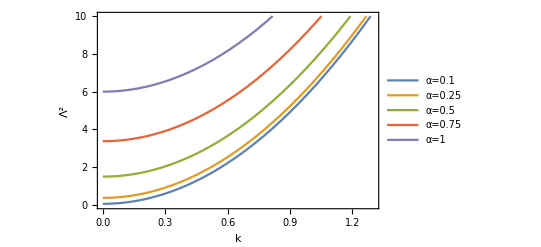

```mathematica
Plot[{LAMBDA0[0.1,k],LAMBDA0[0.25,k],LAMBDA0[0.5,k],LAMBDA0[0.75,k],LAMBDA0[1,k]},{k,0,2},PlotLegends->{"α=0.1","α=0.25","α=0.5","α=0.75","α=1"},Frame->True,Axes->True,FrameLabel->{"k","Λ^2"},PlotRange->{{0,1.3},{0,10}}]
```

### 2

```mathematica
ClearAll[F2]
```

```mathematica
Solve[1/a^2 delta^2 (-a^2 k modofc Q1^2 Sin[2 k z]+k^3 modofc Q1^2 Sin[2 k z]-4 a^2 k modofc Q0 Q2 Sin[2 k z])==-3 delta^2 (lambda1 A[t] Sin[2 k z] w1[0]+A[t]^2 Sin[2 k z] w2[0]),F2]
```

{{F2→(7 a^4+24 a^2 k^2+65 k^4)/(96 k^2 (a^2+k^2))}}

```mathematica
F2:=(7 a^4+24 a^2 k^2+65 k^4)/(96 k^2 (a^2+k^2))
```

```mathematica
FullSimplify[-3/4 delta^3 (lambda1^2 A[t] Sin[k z] w1[0]-4 lambda2 A[t] Sin[k z] w1[0]+8 lambdam A[t] Sin[k z] w1[0]+4 lambda1 A[t]^2 Sin[k z] w2[0]+4 A[t]^3 Sin[k z] w31[0]+4 Sin[k z] w33[0] A'[t])==+1/a^2 delta^3 (-a^2 k modofc Q1 Q2 Sin[k z]-2 k^3 modofc Q1 Q2 Sin[k z]-2 a^2 k modofc Q0 Q3 Sin[k z]-2 a^2 k modofc Q1 Qm Sin[k z])]
```

1/(k (a^2+k^2))delta Sin[k z] (24576 k^4 (a^2+k^2)^2 Lmdhat A[t]-(14 a^6+297 a^4 k^2+652 a^2 k^4-207 k^6) A[t]^3-9216 k^2 (a^2+k^2)^2 A'[t])==0

```mathematica
Collect[Solve[1/(k (a^2+k^2))delta Sin[k z] (24576 k^4 (a^2+k^2)^2 Lmdhat A[t]-(14 a^6+297 a^4 k^2+652 a^2 k^4-207 k^6) A[t]^3-9216 k^2 (a^2+k^2)^2 A'[t])==0,A'[t]],A[t],Simplify]
```

{{A'[t]→8/3 k^2 Lmdhat A[t]-((14 a^6+297 a^4 k^2+652 a^2 k^4-207 k^6) A[t]^3)/(9216 k^2 (a^2+k^2)^2)}}

```mathematica
TranspirationCoeff[a_,k_]:=-(14 a^6+297 a^4 k^2+652 a^2 k^4-207 k^6)/(9216 k^2 (a^2+k^2)^2)
```

```mathematica
Plot3D[TranspirationCoeff[a,k],{a,0.005,0.06},{k,0.005,0.06},ColorFunction->"Rainbow",PlotRange->All,Mesh->All,AxesLabel->{"α","k"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ALTTCoef[gama_]:=-(14 gama^6+297 gama^4+652 gama^2-207)/(9216 (gama^2+1)^2)
```

```mathematica
N[ALTTCoef[0]]
```

0.0224609

```mathematica
N[Solve[ALTTCoef[gama]==0,gama]]
```

{{gama→0.-4.32187 ⅈ},{gama→0.+4.32187 ⅈ},{gama→0.-1.67831 ⅈ},{gama→0.+1.67831 ⅈ},{gama→-0.530124},{gama→0.530124}}

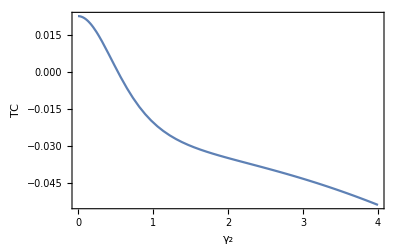

```mathematica
Plot[ALTTCoef[gama],{gama,0,4},PlotRange->All,Frame->True,Axes->True,AxesLabel->{"γ_2","TC"}]
```

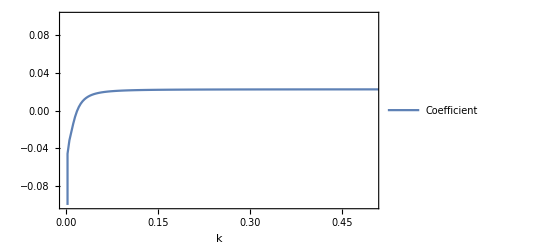

```mathematica
Plot[TranspirationCoeff[0.01,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotLegends->{"Coefficient"},PlotRange->{{0,0.5},{-0.1,0.1}}]
```

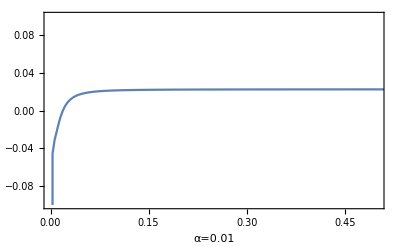
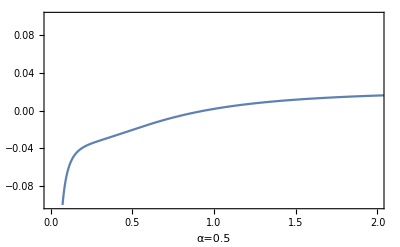
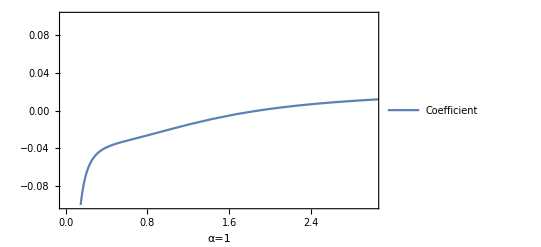

```mathematica
Flatten[Table[{{Plot[TranspirationCoeff[0.01,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,0.5},{-0.1,0.1}},FrameLabel->{"α=0.01"}]},{Plot[TranspirationCoeff[0.5,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.1,0.1}},FrameLabel->{"α=0.5"}]},{Plot[TranspirationCoeff[1,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotLegends->{"Coefficient"},PlotRange->{{0,3},{-0.1,0.1}},FrameLabel->{"α=1"}]}},1]]
```

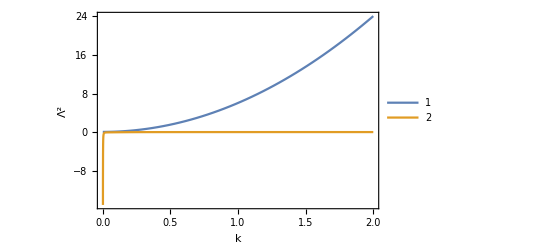

```mathematica
Plot[{LAMBDA0[a,k]/.a->0.1,TranspirationCoeff[a,k]/.a->0.1},{k,0,2},PlotLegends->Automatic,Frame->True,Axes->Automatic,FrameLabel->{"k","Λ^2"}]
```